```mathematica
ChromaticPolynomial[CycleGraph[3],k]
```

ChromaticPolynomial[-Graphics-,k]

```mathematica
ContainsVertex[graph_,vertex_]:=Length[Select[graph,#==vertex || #[[1]]==vertex || #[[2]]==vertex&]]>0
```

```mathematica
Z[graph_]:=Z[graph]=Module[
{ i,l =Length[graph], start, end, meltVertices, dropEdge},
If[l==0,Return[0]];
(* Rule1: Simple graph *)
If[l==1&&IntegerQ[graph[[1]]],
Return[q]
];
(* Rule2 : search for an integer in the graph *)
i=1;
For[i==1,i≤l,i++,
If[IntegerQ[graph[[i]]],
Return[ q * Z[Drop[graph,{i}]]]
]
];
(* Rule 3 : drop an edge *)
start = graph[[1]][[1]];
end = graph[[1]][[2]];
PrintTemporary[{"drop ", start,end} ];
dropEdge=Drop[graph,{1}];
If[!ContainsVertex[dropEdge,start], dropEdge= Join[{start},dropEdge]];
If[!ContainsVertex[dropEdge,end], dropEdge= Join[{end},dropEdge]];
meltVertices=ReplaceAll[Drop[graph,{1}],start->end];
PrintTemporary[{"meltVertices1",meltVertices}];
If[!ContainsVertex[meltVertices,end], meltVertices= Join[{end},meltVertices]];
(*meltVertices=Map[If[#[[1]]==#[[2]],#[[1]],#]&,meltVertices];*)
(*Print[Graph[dropEdge,VertexLabels->"Name"]+v*Graph[meltVertices,VertexLabels->"Name"]];*)
PrintTemporary[{"dropEdge",dropEdge}];
PrintTemporary[{"meltVertices",meltVertices}];
Return[Z[dropEdge]+v*Z[meltVertices]];
]
```

```mathematica
Z2[graph_]:=Z2[graph]=Module[
{ i,l =Length[graph], start, end, meltVertices, dropEdge},
If[l==0,Return[0]];
(* Rule1: Simple graph *)
If[l==1&&IntegerQ[graph[[1]]],
Return[4]
];
(* Rule2 : search for an integer in the graph *)
i=1;
For[i==1,i≤l,i++,
If[IntegerQ[graph[[i]]],
Return[ 4 * Z2[Drop[graph,{i}]]]
]
];
(* Rule 3 : drop an edge *)
start = graph[[1]][[1]];
end = graph[[1]][[2]];
PrintTemporary[{"drop ", start,end} ];
dropEdge=Drop[graph,{1}];
If[!ContainsVertex[dropEdge,start], dropEdge= Join[{start},dropEdge]];
If[!ContainsVertex[dropEdge,end], dropEdge= Join[{end},dropEdge]];
meltVertices=ReplaceAll[Drop[graph,{1}],start->end];
PrintTemporary[{"meltVertices1",meltVertices}];
If[!ContainsVertex[meltVertices,end], meltVertices= Join[{end},meltVertices]];
(*meltVertices=Map[If[#[[1]]==#[[2]],#[[1]],#]&,meltVertices];*)
(*Print[Graph[dropEdge,VertexLabels->"Name"]+v*Graph[meltVertices,VertexLabels->"Name"]];*)
PrintTemporary[{"dropEdge",dropEdge}];
PrintTemporary[{"meltVertices",meltVertices}];
Return[Z2[dropEdge]-Z2[meltVertices]];
]
```

```mathematica
Explain[graph_]:=Module[
{ i,l =Length[graph], start, end, meltVertices, dropEdge, sub, sub2},
If[l==0,Return[0]];
(* Rule1: Simple graph *)
If[l==1&&IntegerQ[graph[[1]]],
Return[{graph->{q}}]
];
(* Rule2 : search for an integer in the graph *)
i=1;
For[i==1,i≤l,i++,
If[IntegerQ[graph[[i]]],
sub=Explain[Drop[graph,{i}]];
Return[ Join[sub,{graph->First[Last[sub]]}]]
]
];
(* Rule 3 : drop an edge *)
start = graph[[1]][[1]];
end = graph[[1]][[2]];
PrintTemporary[{"drop ", start,end} ];
dropEdge=Drop[graph,{1}];
If[!ContainsVertex[dropEdge,start], dropEdge= Join[{start},dropEdge]];
If[!ContainsVertex[dropEdge,end], dropEdge= Join[{end},dropEdge]];
meltVertices=ReplaceAll[Drop[graph,{1}],start->end];
PrintTemporary[{"meltVertices1",meltVertices}];
If[!ContainsVertex[meltVertices,end], meltVertices= Join[{end},meltVertices]];
(*meltVertices=Map[If[#[[1]]==#[[2]],#[[1]],#]&,meltVertices];*)
sub =Explain[dropEdge];
sub2= Explain[meltVertices];
Print[{MyGraph[graph] ,{"drop ", start,end},First[Last[sub]]+v*First[Last[sub2]]}];
Return[Join[sub,sub2,{graph->First[Last[sub]],graph->First[Last[sub]]}]];
]
```

```mathematica
MyGraph[graph_]:=Module[
{i,l =Length[graph], newGraph},
i=1;
newGraph = Map[If[!ListQ[#] ,#->#,#]&,graph];
Graph[newGraph,VertexLabels->"Name"]
]
```

```mathematica
MyGraph[{q}]
```

-Graphics-

```mathematica
Explain[{1->2,2->3,3->1}]
```

{-Graphics-,{drop ,3,1},{v}+{1,3}}

{-Graphics-,{drop ,3,1},{v}+{1,3}}

{-Graphics-,{drop ,2,3},{v (3→1)}+{2,3→1}}

{-Graphics-,{drop ,3,2},{2 v}+{2,3}}

{-Graphics-,{drop ,3,3},{3+3 v}}

{-Graphics-,{drop ,2,3},{(3→2)+v (3→3)}}

{-Graphics-,{drop ,1,2},{(2→3)+v (2→3),(3→1)+v (3→2)}}

{{3}→{q},{1,3}→{3},{1}→{q},{3→1}→{1,3},{3→1}→{1,3},{2,3→1}→{3→1},{3}→{q},{1,3}→{3},{1}→{q},{3→1}→{1,3},{3→1}→{1,3},{2→3,3→1}→{2,3→1},{2→3,3→1}→{2,3→1},{3}→{q},{2,3}→{3},{2}→{q},{3→2}→{2,3},{3→2}→{2,3},{3}→{q},{3}→{q},{3→3}→{3},{3→3}→{3},{2→3,3→2}→{3→2},{2→3,3→2}→{3→2},{1→2,2→3,3→1}→{2→3,3→1},{1→2,2→3,3→1}→{2→3,3→1}}

```mathematica
GraphPlot[Map[MyGraph[#[[1]]]->MyGraph[#[[2]]]&,{{3}->{q},{1,3}->{3},{1}->{q},{3->1}->{1,3},{3->1}->{1,3},{2,3->1}->{3->1},{3}->{q},{1,3}->{3},{1}->{q},{3->1}->{1,3},{3->1}->{1,3},{2->3,3->1}->{2,3->1},{2->3,3->1}->{2,3->1},{3}->{q},{2,3}->{3},{2}->{q},{3->2}->{2,3},{3->2}->{2,3},{3}->{q},{3}->{q},{3->3}->{3},{3->3}->{3},{2->3,3->2}->{3->2},{2->3,3->2}->{3->2},{1->2,2->3,3->1}->{2->3,3->1},{1->2,2->3,3->1}->{2->3,3->1}}],VertexLabeling->True, EdgeLabeling->True]
```

-Graphics-

```mathematica
Graph[{{1->2,2->3,3->1}->{v (q^2+q v+v (q+q v))+({2->3,3->1}->{v (q^2+q v)+({2,3->1}->{q ({3->1}->{q v+({1,3}->{q ({3}->q)})})})})}}]
```

-Graphics-

```mathematica
Explain[{1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6}]
```

{-Graphics-,{drop ,1,4},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,1,5},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,1,6},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,2,4},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,2,5},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,2,6},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,3,4},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,3,5},-Graphics-+-Graphics- v}

{-Graphics-,{drop ,3,6},-Graphics-+-Graphics- v}

q (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))+v (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))+v (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))+v (q (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v)))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v)))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))))+v (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))+v (q (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))+v (q (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))+v (q (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))))

```mathematica
Explain[{1->2}]
```

{-Graphics-,v Graph[{2},VertexLabels→Name]+Graph[{2,1},VertexLabels→Name]}

q^2+q v

```mathematica
Z2[{1->2,1->3,1->4,2->3,2->4,3->4}]
```

24

```mathematica
CompleteGraph[4]
```

-Graphics-

```mathematica
Z[{1->2,2->2}]
```

q (q+q v)+v (q+q v)

```mathematica
Expand[Z[{1->2,1->3,1->4,2->3,2->4,3->4}]]
```

q^4+6 q^3 v+15 q^2 v^2+16 q v^3+4 q^2 v^3+15 q v^4+6 q v^5+q v^6

```mathematica
Expand[Z[{1->2,1->3,1->4,1->5,2->3,2->4,2->5,3->4,3->5,4->5}]]
```

q^5+10 q^4 v+45 q^3 v^2+110 q^2 v^3+10 q^3 v^3+125 q v^4+85 q^2 v^4+222 q v^5+30 q^2 v^5+205 q v^6+5 q^2 v^6+120 q v^7+45 q v^8+10 q v^9+q v^10

```mathematica
K5[q_,v_]:=q^5+10 q^4 v+45 q^3 v^2+110 q^2 v^3+10 q^3 v^3+125 q v^4+85 q^2 v^4+222 q v^5+30 q^2 v^5+205 q v^6+5 q^2 v^6+120 q v^7+45 q v^8+10 q v^9+q v^10
```

```mathematica
Graph[{1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6}]
```

-Graphics-

```mathematica
Expand[Z[{1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6}]]
```

q^6+9 q^5 v+36 q^4 v^2+84 q^3 v^3+117 q^2 v^4+9 q^3 v^4+81 q v^5+45 q^2 v^5+78 q v^6+6 q^2 v^6+36 q v^7+9 q v^8+q v^9

```mathematica
K33[q_,v_]:=q^6+9 q^5 v+36 q^4 v^2+84 q^3 v^3+117 q^2 v^4+9 q^3 v^4+81 q v^5+45 q^2 v^5+78 q v^6+6 q^2 v^6+36 q v^7+9 q v^8+q v^9
```

```mathematica
Z2[{1->2,1->3,1->4,1->5,2->3,2->4,2->5,3->4,3->5,4->5}]
```

```mathematica
K33[4,-1]
```

420

```mathematica
With[{v=-1,q=4},q (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))+v (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))+v (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))+v (q (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v)))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v)))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))))+v (q (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v+v (q+q v))+v (q^2+q v+v (q+q v))))+v (q (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))+v (q (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v))+v (q (q^2+q v)+v (q^2+q v)+v (q (q+q v)+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))+v (q (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q (q^2+q v)+v (q^2+q v)+v (q^2+q v+v (q^2+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))))+v (q (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v)))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))+v (q^2+q v+v (q+q v)+v (q+q v+v (q+q v))))))))]
```

420

```mathematica
Z[3->3]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

q^2

```mathematica
Conjunction[q^4+6 q^3 v+15 q^2 v^2+16 q v^3+4 q^2 v^3+15 q v^4+6 q v^5+q v^6]
```

Conjunction[q^4+6 q^3 v+15 q^2 v^2+16 q v^3+4 q^2 v^3+15 q v^4+6 q v^5+q v^6]

```mathematica
With[{v=-1,q=5},q^4+6 q^3 v+15 q^2 v^2+16 q v^3+4 q^2 v^3+15 q v^4+6 q v^5+q v^6]
```

120

```mathematica
K33[4,-1]
```

420

```mathematica
Plot3D[K33[q,v],{q,0,5},{v,-0.9,-1.1}]
```

-Graphics3D-

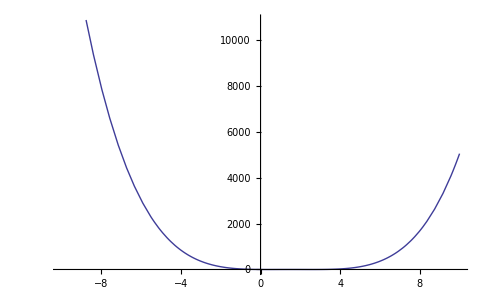

```mathematica
With[{v=-1},Plot[q^4+6 q^3 v+15 q^2 v^2+16 q v^3+4 q^2 v^3+15 q v^4+6 q v^5+q v^6,{q,-10,10}]]
```